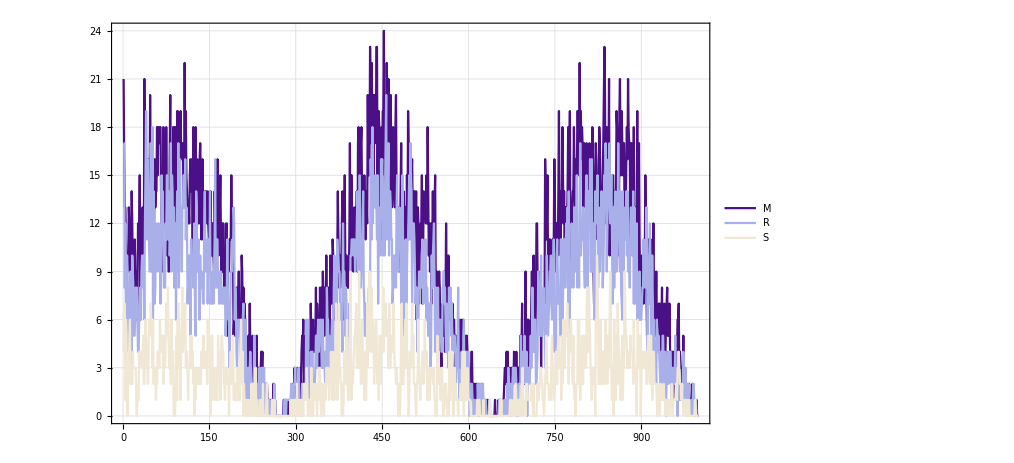
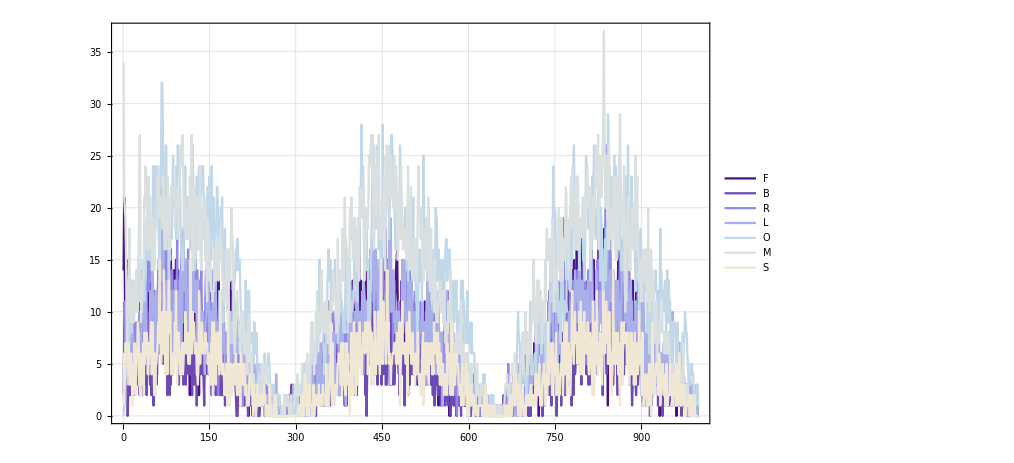

```mathematica
(*Import and Setup Data*)
folder=NotebookDirectory[]<>"Debug/Mosquito/";
raw={mRaw,fRaw}=Import[(folder<>#)]&/@{"MaleMosquitoPop_Run1.csv","FemaleMosquitoPop_Run1.csv"};
head={mHead,fHead}=(#[[1,2;;All]])&/@{mRaw,fRaw};
data={mData,fData}=(#[[2;;All,2;;All]])&/@{mRaw,fRaw};
(**)
plots=ListLinePlot[#[[1]]//Transpose,
PlotRange->{0,All},
Frame->True,
FrameStyle->Directive[Gray,Thick],
GridLines->Automatic,
PlotLegends->#[[2]],
PlotStyle->"LakeColors",
ImageSize->750
]&/@Transpose[{data,head}];
Grid[{{}}]
```